```mathematica
B0[x_]:=BernsteinBasis[3,0,x]
B1[x_]:=BernsteinBasis[3,1,x]
B2[x_]:=BernsteinBasis[3,2,x]
B3[x_]:=BernsteinBasis[3,3,x]
```

```mathematica
D[B1[x],x]
```

3 (BernsteinBasis[2,0,x]-BernsteinBasis[2,1,x])

```mathematica
B0X[x_]=D[B0[x],x]
B1X[x_]=D[B1[x],x]
B2X[x_]=D[B2[x],x]
B3X[x_]=D[B3[x],x]
```

-3 BernsteinBasis[2,0,x]

3 (BernsteinBasis[2,0,x]-BernsteinBasis[2,1,x])

3 (BernsteinBasis[2,1,x]-BernsteinBasis[2,2,x])

3 BernsteinBasis[2,2,x]

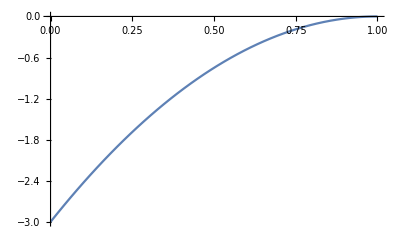

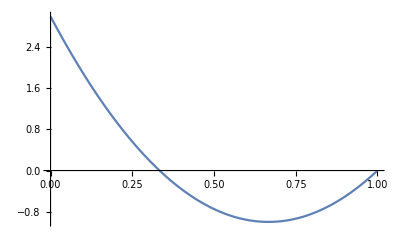

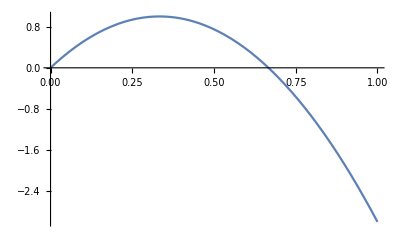

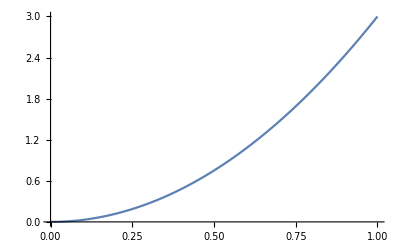

```mathematica
Plot[B0X[x],{x,0,1}]
Plot[B1X[x],{x,0,1}]
Plot[B2X[x],{x,0,1}]
Plot[B3X[x],{x,0,1}]
```

```mathematica
B0XX[x_]=D[B0X[x],x]
B1XX[x_]=D[B1X[x],x]
B2XX[x_]=D[B2X[x],x]
B3XX[x_]=D[B3X[x],x]
```

6 BernsteinBasis[1,0,x]

3 (-2 BernsteinBasis[1,0,x]-2 (BernsteinBasis[1,0,x]-BernsteinBasis[1,1,x]))

3 (2 (BernsteinBasis[1,0,x]-BernsteinBasis[1,1,x])-2 BernsteinBasis[1,1,x])

6 BernsteinBasis[1,1,x]

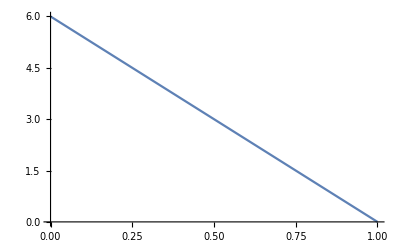

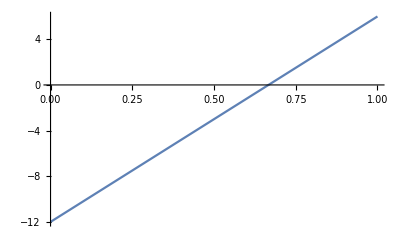

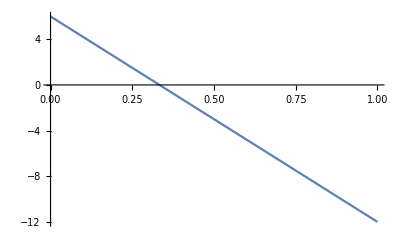

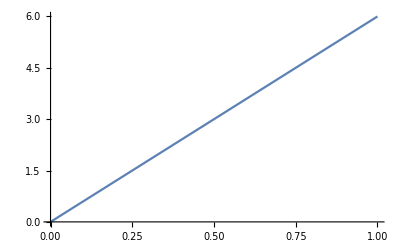

```mathematica
Plot[B0XX[x],{x,0,1}]
Plot[B1XX[x],{x,0,1}]
Plot[B2XX[x],{x,0,1}]
Plot[B3XX[x],{x,0,1}]
```